```mathematica
Clear[x,y]
f[x_,y_]=Cos[2x+y]+x-y;
```

```mathematica
a=0;b=1;h1=0.1;h2=0.05;n1=Floor[(b-a)/h1];n2=Floor[(b-a)/h2];x0=0;y0=0;
```

```mathematica
x0=0;y0=0;
eulk1=Table[{x0,y0}={x0+h1,y0+h1/2*(f[x0,y0]+f[x0+h1,y0+h1*f[x0,y0]])},{i,0,n1-1}]
```

{{0.1,0.0977668},{0.2,0.187446},{0.3,0.263262},{0.4,0.322246},{0.5,0.363954},{0.6,0.389755},{0.7,0.402083},{0.8,0.403856},{0.9,0.39812},{1.,0.387867}}

```mathematica
eulk1//Column
```

{0.1,0.0977668}
{0.2,0.187446}
{0.3,0.263262}
{0.4,0.322246}
{0.5,0.363954}
{0.6,0.389755}
{0.7,0.402083}
{0.8,0.403856}
{0.9,0.39812}
{1.,0.387867}

```mathematica
eulk1=Prepend[eulk1,{0,0}]
```

{{0,0},{0.1,0.0977668},{0.2,0.187446},{0.3,0.263262},{0.4,0.322246},{0.5,0.363954},{0.6,0.389755},{0.7,0.402083},{0.8,0.403856},{0.9,0.39812},{1.,0.387867}}

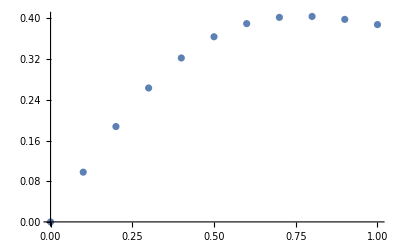

```mathematica
gr1=ListPlot[eulk1]
```

```mathematica
x0=0;y0=0;
eulk2=Table[{x0,y0}={x0+h2,y0+h2/2*(f[x0,y0]+f[x0+h2,y0+h2*f[x0,y0]])},{i,0,n2-1}]
```

{{0.05,0.0497193},{0.1,0.0983568},{0.15,0.14494},{0.2,0.188643},{0.25,0.228815},{0.3,0.264989},{0.35,0.296877},{0.4,0.324352},{0.45,0.347434},{0.5,0.366255},{0.55,0.381039},{0.6,0.392075},{0.65,0.3997},{0.7,0.404279},{0.75,0.406191},{0.8,0.405823},{0.85,0.403563},{0.9,0.399792},{0.95,0.394883},{1.,0.389205}}

```mathematica
eulk2=Prepend[eulk2,{0,0}]
```

{{0,0},{0.05,0.0497193},{0.1,0.0983568},{0.15,0.14494},{0.2,0.188643},{0.25,0.228815},{0.3,0.264989},{0.35,0.296877},{0.4,0.324352},{0.45,0.347434},{0.5,0.366255},{0.55,0.381039},{0.6,0.392075},{0.65,0.3997},{0.7,0.404279},{0.75,0.406191},{0.8,0.405823},{0.85,0.403563},{0.9,0.399792},{0.95,0.394883},{1.,0.389205}}

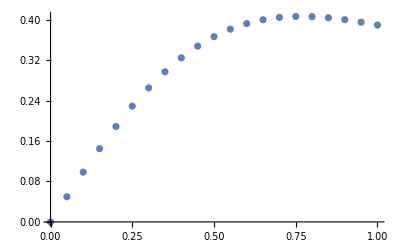

```mathematica
gr2=ListPlot[eulk2]
```

```mathematica
(*б)Метод Рунге-Кутта*)
```

```mathematica
Clear[x,y]
f[x_,y_]=Cos[2x+y]+x-y;
a=0;b=1;x0=0;y0=0;h1=0.1;h2=0.05;n1=Floor[(b-a)/h1];n2=Floor[(b-a)/h2];
```

```mathematica
sol1=List[{x0,y0}];
```

```mathematica
x=x0;y=y0;
For[k=1,k<n1+1,k++,
k1[x_,y_]=h1*f[x,y];
k2[x_,y_]=h1*f[x+h1/2,y+k1[x,y]/2];
k3[x_,y_]=h1*f[x+h1/2,y+k2[x,y]/2];
k4[x_,y_]=h1*f[x+h1,y+k3[x,y]];
x=x+h1;
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol1=Append[sol1,{x,y}]]
```

```mathematica
sol1
```

{{0,0},{0.1,0.0985514},{0.2,0.18903},{0.3,0.265538},{0.4,0.325013},{0.5,0.36697},{0.6,0.392791},{0.7,0.404951},{0.8,0.406423},{0.9,0.400298},{1.,0.389606}}

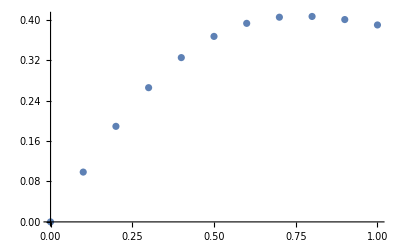

```mathematica
gr3=ListPlot[sol1]
```

```mathematica
(*с помощью функций DSolve и NDSolve,построить графики.*)
```

```mathematica
Clear[so12]
sol2=List[{x0,y0}];
```

```mathematica
x=x0;y=y0;
For[k=1,k<n2+1,k++,
k1[x_,y_]=h2*f[x,y];
k2[x_,y_]=h2*f[x+h2/2,y+k1[x,y]/2];
k3[x_,y_]=h2*f[x+h2/2,y+k2[x,y]/2];
k4[x_,y_]=h2*f[x+h2,y+k3[x,y]];
x=x+h2;
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol2=Append[sol2,{x,y}]]
```

```mathematica
sol2
```

{{0,0},{0.05,0.0498153},{0.1,0.0985519},{0.15,0.145233},{0.2,0.189031},{0.25,0.22929},{0.3,0.265541},{0.35,0.297491},{0.4,0.325016},{0.45,0.348132},{0.5,0.366973},{0.55,0.381764},{0.6,0.392795},{0.65,0.400403},{0.7,0.404955},{0.75,0.406834},{0.8,0.406427},{0.85,0.404122},{0.9,0.400301},{0.95,0.395341},{1.,0.389609}}

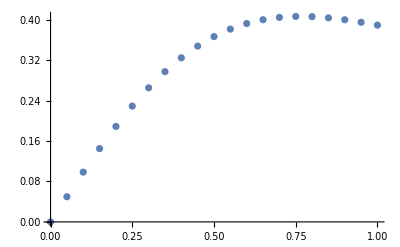

```mathematica
gr4=ListPlot[sol2]
```

```mathematica
Clear[y,x]  (*Очистка предыдущих определений*)
eqn=y'[x]==x+Cos[2x+y[x]]-y[x];
initialCondition=y[0]==0;
solutionDSolve=DSolve[{eqn,initialCondition},y,x];
y1[x_]=y[x]/.Flatten[solutionDSolve]
Print["Аналитическое решение: ",solutionDSolve];3
```

y[x]/.DSolve[{y'[x]==x+Cos[2 x+y[x]]-y[x],y[0]==0},y,x]

Аналитическое решение: DSolve[{y'[x]==x+Cos[2 x+y[x]]-y[x],y[0]==0},y,x]

```mathematica
Clear[y,x]  (*Очистка предыдущих определений*)
eqn=y'[x]==x+Cos[2x+y[x]]-y[x];
initialCondition=y[0]==0;
solutionNDSolve=NDSolve[{eqn,initialCondition},y,{x,0,1}]
```

{{y→InterpolatingFunction[…]}}

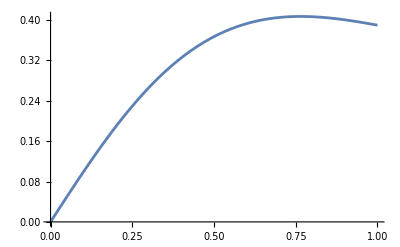

```mathematica
gr5=Plot[Evaluate[y[x]/.solutionNDSolve],{x,0,1}]
```

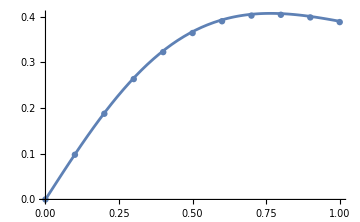

```mathematica
Show[gr1,gr5,ImageSize->Medium]
```

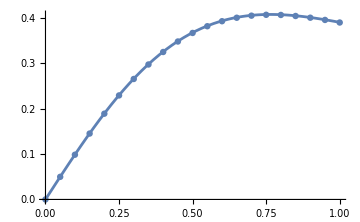

```mathematica
Show[gr2,gr5,ImageSize->Medium]
```

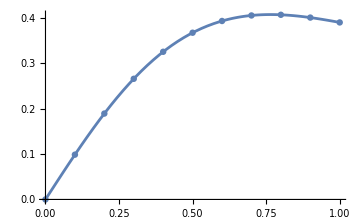

```mathematica
Show[gr3,gr5,ImageSize->Medium]
```

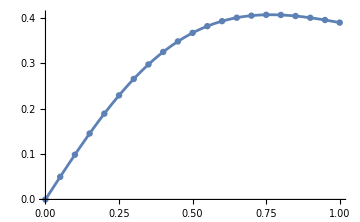

```mathematica
Show[gr4,gr5,ImageSize->Medium]
```